# Wolfram Language Summer School Project

## Machine Learning & Data Protection Paris-Saclay Jaafar Rammal & Natael Baffou

## Outline

SideNotes cell

SideNotes and SideCode cells will not show during presentation.

Machine Learning:

Financial predictions

Interactive classification

Data protection

Concepts of Steganography and Encryption

Project demonstration

```mathematica
Machine Learning
```

### Financial Predictions

The program goal is to predict stocks values with training sets missing recent periods

Example:
- Train the network on dataset from Jan 2000 till Jan 2018
- Skip the Feb 2018
- Predict the Mar 2018 dataset
- Plot the different information

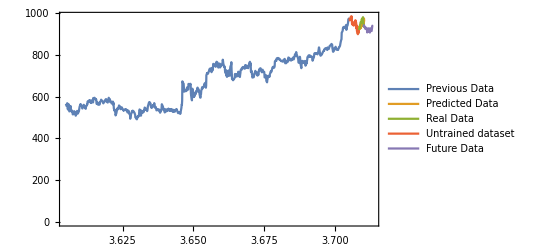

The code:

```mathematica
company = "EBAY";
fct[data_]:= {DateObject[data[[1]]] -> data[[2]]}
training = FinancialData[company,{"Jan. 1, 2000","May. 30, 2017"}];
pp = Flatten[Table[fct[training[[n]]],{n,1,Length[training]}]];
Function[data,{DateObject[data[[1]]]->data[[2]]}];
p= Predict[pp, Method->"NearestNeighbors"];
map[date_][{data_}] := {date,data};
predictvalues = Table[map[{2017,7,n}][p[{DateObject[{2017,7,n}]}]],{n,1,30}];
DateListPlot[{training,predictvalues,FinancialData[company,{"Jul. 1, 2017","Jul. 30, 2017"}],FinancialData[company,{"May. 29, 2017","Jul. 9,2017"}],FinancialData[company,{"Jul. 27, 2017","Sep. 1, 2017"}]},PlotLegends->{"Previous Data","Predicted Data","Real Data","Untrained dataset","Future Data"}]
```

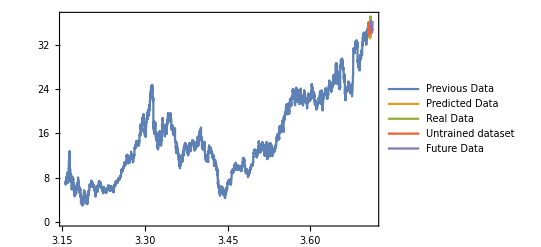

## Interactive Classification

This program allows the user to train the computer on recognizing persons or objects and naming them after being trained, using the Wolfram Function “Classify”

### Overview

It is composed of different parts:
- External folder containing training-set images
- Funtions to monitor the imports and the neural network
- Dynamic update of the input image from the camera
- Interactive user panel

### Flow chart

A summary of the program’s behavior:

			-Graphics-

Demonstration

```mathematica
dir = Environment["HOME"]<>"/Desktop/Faces/";
If[DirectoryQ[ToString[dir]],,CreateDirectory[ToString[dir]]];
SetDirectory[ToString[dir]];
f[name_] := {Import[name]-> StringReplace[name, Flatten[{ToString[dir]->"",".JPG"->"", Table[ToString[x]->"", {x, 0, 9}]}]]}
trainingSet = Flatten[Map[f, FileNames["*",ToString[dir]]]];
tr = Classify[trainingSet];
Dynamic[img = ImageReflect[CurrentImage[],Left]]
Panel[Row[{InputField[Dynamic[Name]],Button["Take Picture",Export[ToString[Name]<>""<>ToString[Count[StringReplace[FileNames["*",ToString[dir]],{ToString[dir]->"",".JPG"->""}],v_/;StringMatchQ[v,ToString[Name]<>"*"]]+1]<>".JPG",img]],Button["Stop",DeviceClose[Devices[][[1]]]],Button["Train",tr=Classify[trainingSet]]Dynamic[tr[img]],"    ",Dynamic[tr[img,"Probabilities"]]}]]
```

Take PictureStopTrain

## DATA PROTECTION

Data protection has always been an important issue, and there are many ways to encrypt data or hide it

#### Concepts of Encryption and Steganography

### Data encryption: Changing the data

Encrypting data involves by definition changing its value, following a specific pattern.
There are multiple data-encryption methods. We have chosen two basic methods: the Caesar Encryption and the Vigenere Encryption.

### Steganography: Concealing data

Steganography is about hiding data within another data set without altering its original value.
(Example: Hiding a text in an image through pixel operations or in an audio file through Fourrier operations)

## Project Structure

Our project consists of a simple interface that allows the user to encrypt a message or / and hide it into an image

		     -Graphics-

The user interacts with the program through text fields and buttons

## From theory to concrete application

How do the different used systems behave and how do we translate them into wolfram code?

### Caesar

The cesar encryption follow a basic “shifiting” process as shown below

					-Graphics-

```mathematica
cesarEncode[text_, pos_] := FromCharacterCode[Mod[ToCharacterCode[text] + pos, 256]]
cesarDecode[text_, pos_] := FromCharacterCode[Mod[ToCharacterCode[text] - pos, 256]]
demo = cesarEncode["ABCD",10]
cesarDecode[demo,10]
```

KLMN

ABCD

### Vigenere

The vigenere encryption behaves through adding the values of a text key

```mathematica
vigenereEncode[text_, key_] := FromCharacterCode[Mod[ToCharacterCode[text]+ToCharacterCode[StringJoin[{Table[key, {n, 1, Floor[StringLength[text]/StringLength[key]]}], StringTake[key, Mod[StringLength[text], StringLength[key]]]}]], 256]]

vigenereDecode[text_, key_] := FromCharacterCode[Mod[ToCharacterCode[text]-ToCharacterCode[StringJoin[{Table[key, {n, 1, Floor[StringLength[text]/StringLength[key]]}], StringTake[key, Mod[StringLength[text], StringLength[key]]]}]], 256]]

demo = vigenereEncode["1234","AB"]
demo = vigenereEncode["2345","AB"]
```

rttv

suuw

### Steganography

-Graphics-
1: ASCII Code of letter “e”
2: Original pixel codes
3: New pixel codes

```mathematica
hideMessage[textToHide_,carrierImageLink_,offset_]:=
(
img = Import[ToString[carrierImageLink]];
imgdata= ImageData[img,"Byte"];
bitFormOfMessage = ImportString[ToString[textToHide],{"Bit"}];
fimg = Flatten[imgdata];
For[i=1,i≤Length[bitFormOfMessage],i++,fimg[[i+offset*8]]=hide[bitFormOfMessage[[i]],fimg[[i+offset*8]]]];
Image[Partition[Partition[fimg,3],Length[imgdata[[1]]]],"Byte"]
)
```

## Main code and final product

### PS: “FREE TExT” option under construction

```mathematica
(* BEGINNING of the encryption functions *)

(* Definition of the crypt and decrypt funtion*)

crypt[textToCrypt_, "Cesar", offset_]:= cesarEncode[textToCrypt, offset]
crypt[textToCrypt_, "Vigenere",  key_]:=vigenereEncode[textToCrypt, key]
crypt[textToCrypt_, "Free Text", no_] := textToCrypt
decrypt[textToDecrypt_, "Cesar", offset_]:= cesarDecode[textToDecrypt, offset]
decrypt[textToDecrypt_, "Vigenere", key_]:=vigenereDecode[textToDecrypt, key]
crypt[textToDecrypt_, "Free Text", no_] := textToDecrypt

(* Definition of the Cesar encoding and decoding *)

cesarEncode[text_, pos_] := FromCharacterCode[Mod[ToCharacterCode[text] + pos, 256]]
cesarDecode[text_, pos_] := FromCharacterCode[Mod[ToCharacterCode[text] - pos, 256]]

(* Definition of the  vigenere encoding and decoding *)

vigenereEncode[text_, key_] := FromCharacterCode[Mod[ToCharacterCode[text]+ToCharacterCode[StringJoin[{Table[key, {n, 1, Floor[StringLength[text]/StringLength[key]]}], StringTake[key, Mod[StringLength[text], StringLength[key]]]}]], 256]]

vigenereDecode[text_, key_] := FromCharacterCode[Mod[ToCharacterCode[text]-ToCharacterCode[StringJoin[{Table[key, {n, 1, Floor[StringLength[text]/StringLength[key]]}], StringTake[key, Mod[StringLength[text], StringLength[key]]]}]], 256]]

(* END of the encrytpion functions *)


(*BEGINNING of the steganograph functions *)

(*Common constants and functions, defined externally*)

hide[0,p_?EvenQ]:=p
hide[0,p_?OddQ]:= p+1
hide[1,p_?EvenQ]:= p-1
hide[1,p_?OddQ]:=p

rest[pp_?EvenQ]:=0
rest[pp_?OddQ]:=1

na = "There is no hidden message in this image or you have enterred the wrong input";

(*AssembleMessage function: assemble message + first recognition string + last recognition char*)
(*
Inputs
- Message to hide
- First recognition string
- Last recognition string
*)
(*
Outputs
- One full string ready to be encrypted
*)

assembleMessage[messageToHide_,firstRecognition_,lastRecognition_]:=
(
ToString[firstRecognition]<>ToString[messageToHide]<>ToString[lastRecognition]
)


(*HideMessage function: hides a message in an image and returns the imag*)
(*
Inputs
- The message to hide
- Link to the image where you want to hide the message
- Offset of hiding
- First recognition string
- Last recognition string
*)
(*
Outputs:
- The new image with the hidden message
*)

hideMessage[textToHide_,carrierImageLink_,offset_]:=
(
img = Import[ToString[carrierImageLink]];
imgdata= ImageData[img,"Byte"];
bitFormOfMessage = ImportString[ToString[textToHide],{"Bit"}];
fimg = Flatten[imgdata];
For[i=1,i≤Length[bitFormOfMessage],i++,fimg[[i+offset*8]]=hide[bitFormOfMessage[[i]],fimg[[i+offset*8]]]];
Image[Partition[Partition[fimg,3],Length[imgdata[[1]]]],"Byte"]
)



(*RetrieveText function: retrieves full encrypted text from image*)
(*
Inputs
- Link to the image with the hidden message
*)
(*
Outputs:
- Full converted text with trash chars
*)
retrieveText[carrierImageLink_]:=
(
timg =  Flatten[ImageData[Import[ToString[carrierImageLink]],"Byte"]];ExportString[Partition[Table[rest[timg[[n]]],{n,1,Length[timg]}],8],"Bit"]
)



(*SeparateTextBeginning function: separates the real message from the trash before it*)
(*
Input
- Full text with trash
- First recognition string
*)
(*
Outputs
- The message + the part after
OR
- A user-message of non-available message
*)

separateTextBeginning[text_,firstRecognition_]:=
(

If[StringContainsQ[ToString[text],ToString[firstRecognition]],StringReplace[text,(___~~ToString[firstRecognition]~~w___~~___):>firstRecognition<>w],na]
)




(*SeparateText function: separates the real message from decoded trash through recognition-string filter*)
(*
Input
- Full text with trash
- First recognition string
- Last recognition string
*)
(*
Outputs
- The clean message without the trash
OR
- A user-message of non-available message
*)
separateText[text_,firstRecognition_,lastRecognition_]:=
(
na = "There is no hidden message in this image or you have enterred the wrong key";
If[StringContainsQ[ToString[text],ToString[firstRecognition]],StringReplace[text,(ToString[firstRecognition]~~w___~~ToString[lastRecognition]~~___):>w],na]
)




(*ExportImage function: exports the image to the specified directory*)
(*
Inputs
- The image to export
- The export directory
- The image name
*)
(*
Outputs
- NONE
*)

exportImage[image_,expDir_,expName_]:=
(
Export[ToString[expDir]<>"/"<>ToString[expName]<>".png",Image[image,"Byte"]];
)


(*ExportText function: exports the text to the specified directory*)
(*
Inputs
- The text to export
- The export directory
- The text name
*)
(*
Outputs
- NONE
*)

exportText[text_,expDir_,expName_]:=
(
Export[ToString[expDir]<>"/"<>ToString[expName]<>".txt",text];
)

(*END of the steganograph functions *)

printParameters[codingMethode_, parameters_] := Panel[Column[{}]]



DynamicModule[{vigenereKey = Null, encoding = "Encode", codingMethode = "Free Text", cesarOffset = Null, inputText = Null, outputText="Decoder Output",imageOffset = Null, recoStartString = "1234567", recoEndString = "7654321", filePath = Directory[], exportName = Null, parameters = Null, myImage = -Graphics-, codingSelector = Null, imageEncryptionDisplay = Null, codingSupport = "Text", cryptedMessage = "", noParameters = "0"},Panel[Row[{Panel[Column[{SetterBar[Dynamic[encoding], {"Encode", "Decode"}],Panel[PaneSelector[{"Encode"-> Column[{PopupMenu[Dynamic[codingMethode, (codingMethode = #; parameters = <|"Cesar" -> cesarOffset, "Vigenere"-> vigenereKey, "free Text"-> noParameters|>[codingMethode])&], {"Free Text", "Cesar", "Vigenere"}], InputField[Dynamic[inputText],String, FieldHint->"Your text to code here"],If[codingMethode ≠ "Free Text","Coding methode parameters :", ""],codingSelector = PaneSelector[
{"Cesar"->  Row[{"Offset : ", InputField[Dynamic[cesarOffset , (cesarOffset = #; parameters = cesarOffset)&],Number, FieldHint->1]}],
 "Vigenere"-> Row[{"Key value : ", InputField[Dynamic[vigenereKey, (vigenereKey= #; parameters = vigenereKey)&],String, FieldHint->"Your key"]}],
"Free Text"-> (parameters = noParameters;)},Dynamic[codingMethode]],imageEncryptionDisplay =Dynamic[If[codingSupport ==="Image",Column[{"Image encryption parameters", Dynamic[If[encoding==="Encode",Row[{"Offset : ", InputField[Dynamic[imageOffset],Number, FieldHint->0]}], ""]], Row[{"Starting recognition characters : ", InputField[Dynamic[recoStartString],String, FieldHint->"Characters before text"]}], Row[{"Ending recognition characters : ",InputField[Dynamic[recoEndString],String, FieldHint->"Characters after the text"]}]}], ""]], Button["Encrypt",Which[codingSupport==="Image",myImage=hideMessage[crypt[assembleMessage[inputText, recoStartString, recoEndString], codingMethode, parameters], filePath, imageOffset], codingSupport==="Text",cryptedMessage = crypt[inputText, codingMethode, parameters]]],Row[{InputField[Dynamic[exportName], FieldHint->"Your export file name"],Button["Export", Dynamic[Which[codingSupport==="Image",exportImage[myImage,SystemDialogInput["Directory"],exportName], codingSupport=== "Text", exportText[cryptedMessage, SystemDialogInput["Directory"], exportName]]],Method->"Queued"]}]}],
 "Decode"-> Column[{PopupMenu[Dynamic[codingMethode, (codingMethode = #; parameters = <|"Cesar" -> cesarOffset, "Vigenere"-> vigenereKey, "Free Text"-> noParameters|>[codingMethode])&], {"Free Text","Cesar", "Vigenere"}],Panel[Dynamic[outputText]], If[codingMethode≠ "Free Text", "Decoding methode parameters :", ""],codingSelector,"", imageEncryptionDisplay, Button["Decrypt", outputText = Which[codingSupport==="Image",separateText[decrypt[separateTextBeginning[retrieveText[filePath],crypt[recoStartString, codingMethode, parameters] ], codingMethode, parameters],recoStartString, recoEndString], codingSupport==="Text", decrypt[cryptedMessage, codingMethode, parameters]]]}]}, Dynamic[encoding]], ImageSize-> Full]}],ImageMargins-> 5, ImageSize->{Automatic, {350, 500}}], 
Panel[Column[{SetterBar[Dynamic[codingSupport], {"Text", "Image"}],Panel[PaneSelector[{"Image"-> Column[{Row[{Button["Import", {filePath=SystemDialogInput["FileOpen"], myImage=Import[filePath]},Method->"Queued"]}], Dynamic[Image[myImage, ImageSize-> {Automatic, 250}]]}], "Text"-> Column[{"Your text encrypt : ", InputField[Dynamic[cryptedMessage], String, FieldHint-> "Your encrypted message", Enabled-> Dynamic[Which[encoding==="Encode", False,encoding ==="Decode", True]]]}]}, Dynamic[codingSupport]]]}],ImageMargins-> 5, ImageSize->{Automatic, {350, 500}}]
}]]]
```

## CONCLUSION

### Personal Appreciation

We believe we delivered a great response to our ambitions through our small projects in the limited ammount of time we had.

Our multiple functions could consitute a “library” since they have multiple and independant parameters to gain control over a running process

### Futur ambitions

- Customized neural-network and user interface  for  financial predictions 
- Conceal data in audio files through Fourrier process
- Involving machine learning in data protection

### Project Conclusion

Interactive processes add a layer of simplicity to the use of the Wolfram computing power

## THANK YOU FOR YOUR ATTENTION

Jaafar Rammal
+44 7 7 45054115
jarammal@gmail.com

Natael Baffou
0033783732311
natael.baffou1@gmail.com

### ANY QUESTIONS?